## Prior on localization n1, n2

### Inverse - gamma distribution

```mathematica
(*interval = {0.01, 100};
α=0.001;
β=nScale * (α+1);
(*β=0.18422522996251992;*)
mode = β/(α+1);


p[n_]:=β^α/Gamma[α] n^(-α-1)Exp[-β/n];
Plot[p[n],{n,0, 10}, PlotRange->All]
(p/@interval)/p[mode]//N
Print["Mode = ", β/(α+1)];
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)*)
```

### Gamma distribution

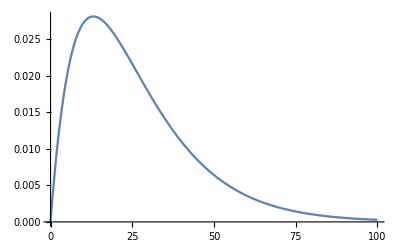

{0.00207473,0.01}

θ = 13.0918

Mode = 13.0918

ns = {10,100,1000} P(ns) = {0.0271813,0.000280999,3.91794×10^-33}

```mathematica
rightBorder=100;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[n_]:=1/(Gamma[k] θ^k)n^(k-1)Exp[- n/θ];
Plot[p[n],{n,0, rightBorder}, PlotRange->All]
(p/@interval)/p[mode]//N
Print["θ = ", θ];
Print["Mode = ", mode];
ns={10,100,1000};
Print["ns = ",ns, " P(ns) = ", p[ns]//N];
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)
```

## Diffusivity prior

### Gamma distribution

```mathematica
rightBorder=5;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[n_]:=1/(Gamma[k] θ^k)n^(k-1)Exp[- n/θ];
Plot[p[n],{n,0, rightBorder}, PlotRange->All]
(p/@interval)/p[mode]//N
Print["θ = ", θ];
Print["Mode = ", mode];
ns={10,100,1000};
Print["ns = ",ns, " P(ns) = ", p[ns]//N];
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)
```

-Graphics-

{0.00207473,0.708597}

θ = 13.0918

Mode = 13.0918

ns = {10,100,1000} P(ns) = {0.0271813,0.000280999,3.91794×10^-33}

Inverse - Gamma distribution. D0 through the mean

{0.1245→0.382212}

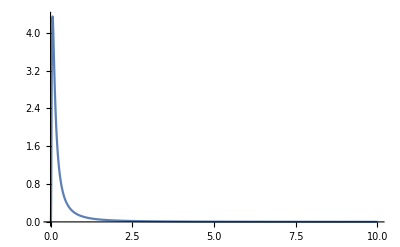

895.13

{0.00487756,0.00485753}

0.00085566

```mathematica
interval = {0.01, 5};
DScale = 0.5;
α=1; 
(*β=DScale * (α+1);*)
β=0.1245;
mode = β/(α+1);
(*τ =1/100;
Clear[β];*)
 dPrior[d_]:=β^α/Gamma[α] d^(-α-1)Exp[-β/d];
sol =FindRoot[dPrior[5]/ dPrior[β/(α+1)]==τ,{β,10^-7,1}]
Plot[dPrior[d]/.sol,{d,0, 10}, PlotRange->All]
dPrior[β/(α+1)]/dPrior[5]
(dPrior/@interval)
dPrior[12]
```

## Link strength

### Gamma distribution for link strength

```mathematica
rightBorder=100;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[n12_]:=1/(Gamma[k] θ^k)n12^(k-1)Exp[- n12/θ];
Plot[p[n12],{n12,0, rightBorder}, PlotRange->All]

(p[rightBorder])/p[mode]
(p[10^3])/p[mode]
(*Print["Var=", α/(α-1) θ^2]*)
```

-Graphics-

0.01

1.39429×10^-31